# De ecuaciones a código

## Estructuras de datos y loops

## Estructuras de datos

En ciencias de la computación, las estructuras de datos son formas de organizar y almacenar datos para que puedan utilizarse de manera eficiente. Definen cómo se organizan los datos en la memoria y cómo se realizan operaciones como el acceso, la inserción, la eliminación y la búsqueda.

En esta sección estudiaremos las estructuras de datos más importantes en Wolfram Language.

### Listas

Una lista es una colección ordenada de elementos encerrados entre llaves { }. Sus elementos pueden ser de cualquier tipo: números, símbolos, expresiones, e incluso otras listas.

```mathematica
lista={3.14,2.72,"hola","mundo",x,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b]}
```

#### Estructura de listas

Podemos acceder a cada elemento de una lista usando la notación de doble corchete ⟦ ⟧. A cada elemento le corresponde un índice comenzando desde el 1 hacia adelante.

```mathematica
Grid[#,
Spacings->{2,1},
Frame->{None,None,{{2,2},{2,Length[#[[2]]]}}->True},
ItemStyle->{Automatic,{Directive[Orange,Bold,FontSize->12]}}
]&@
({Prepend[Range[Length[#]],Null],Prepend[#,"lista ="]}&@lista)
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
lista = | 3.14 | 2.72 | hola | mundo | x | y | {10,20} | {{30,40},{40,50}} | Sin[a] | Cos[b]

```mathematica
lista[[1]]
```

```mathematica
lista[[7]]
```

```mathematica
lista[[7,1]]
```

```mathematica
lista[[-1]]
```

```mathematica
lista[[{1,3,8}]]
```

```mathematica
lista[[2;;4]]
```

```mathematica
lista[[2;;7;;2]]
```

```mathematica
lista[[;;;;2]]
```

Al acceder a los elementos de una lista también podemos sustituir los valores que se encuentran en cada posición.

```mathematica
lista
```

```mathematica
lista[[1]]=π
```

```mathematica
lista
```

Además de los ⟦ ⟧ tenemos otro tipo de operaciones específicas de listas para seleccionar elementos

```mathematica
First[lista]
```

```mathematica
Last[lista]
```

```mathematica
Rest[lista]
```

```mathematica
Most[lista]
```

```mathematica
Take[lista,4]
```

```mathematica
Drop[lista,4]
```

```mathematica
Drop[lista,-4]
```

#### Manipulación de listas

Podemos añadir y quitar valores a las listas usando:

```mathematica
Append[lista,γ]
```

{3.14,2.72,hola,mundo,x,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b],γ}

```mathematica
Prepend[lista,α]
```

{α,3.14,2.72,hola,mundo,x,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b]}

```mathematica
Insert[lista,σ,6]
```

{3.14,2.72,hola,mundo,x,σ,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b]}

```mathematica
Delete[lista,7]
```

{3.14,2.72,hola,mundo,x,y,{{30,40},{40,50}},Sin[a],Cos[b]}

```mathematica
DeleteDuplicates[{4,4,5,2,3,3,1,5,1,1}]
```

{4,5,2,3,1}

```mathematica
lista
```

{3.14,2.72,hola,mundo,x,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b]}

Y sus versiones de programación procedural.

```mathematica
AppendTo[lista,γ]
```

{3.14,2.72,hola,mundo,x,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b],γ}

```mathematica
PrependTo[lista,α]
```

{α,3.14,2.72,hola,mundo,x,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b],γ}

```mathematica
lista
```

{α,3.14,2.72,hola,mundo,x,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b],γ}

Además podemos usar otras funciones sobre nuestras listas

```mathematica
Length[lista]
```

```mathematica
Length[lista[[8]]]
```

```mathematica
Dimensions[lista]
```

```mathematica
Dimensions[lista[[8]]]
```

```mathematica
Flatten[lista]
```

```mathematica
Join[lista,{i,j,k}]
```

```mathematica
Partition[lista,2]
```

```mathematica
Reverse[lista]
```

```mathematica
Sort[{3,12,13,7,7,11,3,4,10,13,11,1,4,5,15}]
```

{1,3,3,4,4,5,7,7,10,11,11,12,13,13,15}

#### Operación de listas

```mathematica
lista={2,6/7,π,ⅈ};
```

```mathematica
lista+1
```

```mathematica
lista+{1,2,3,4}
```

```mathematica
2*lista
```

```mathematica
{1,2,3,4}*lista
```

```mathematica
lista^2
```

```mathematica
lista^{1,2,3,4}
```

```mathematica
Exp[lista]
```

```mathematica
Sin[lista]
```

```mathematica
Log[lista]
```

```mathematica
Total[lista]
```

#### Estadística

```mathematica
lista={7,23,29,65,52,25,30,10,22,31,15,17,5,56,42,25,27,30,15,5,12,16,9,12,13,38,73,28,17,37,84,1,53,44,18,32,7,7,19,10,27,6,22,22,26,5,21,69,24,25,24,34,15,17,16,4,9,4,53,25,18,38,20,4,38,17,44,2,12,40,28,26,19,21,17,52,4,18,8,1,18,45,9,4,84,1,45,13,25,15,55,29,51,22,1,60,9,1,15,25};
```

```mathematica
Min[lista]
```

```mathematica
Max[lista]
```

```mathematica
Mean[lista]
```

```mathematica
N[Mean[lista]]
```

```mathematica
StandardDeviation[lista]
```

```mathematica
StandardDeviation[lista]//N
```

#### Creación de listas

```mathematica
{1,2,3}
```

{1,2,3}

```mathematica
List[1,2,3]
```

{1,2,3}

```mathematica
?Range
```

```mathematica
Range[0,7]
```

{0,1,2,3,4,5,6,7}

```mathematica
?Table
```

```mathematica
Table[a,9]
```

{a,a,a,a,a,a,a,a,a}

```mathematica
Table[i^2,{i,1,10}]
```

```mathematica
Table[i^2,{i,{1,9,6,7}}]
```

{1,81,36,49}

```mathematica
Table[a[i,j],{i,1,3},{j,4,9,2}]
```

{{a[1,4],a[1,6],a[1,8]},{a[2,4],a[2,6],a[2,8]},{a[3,4],a[3,6],a[3,8]}}

```mathematica
?ConstantArray
```

```mathematica
ConstantArray[a,{3,3}]
```

{{a,a,a},{a,a,a},{a,a,a}}

```mathematica
?CenterArray
```

```mathematica
CenterArray[a,{3,3}]
```

{{0,0,0},{0,a,0},{0,0,0}}

### Expresiones

```mathematica
expr=a x^2+b x+c+f[x]+d g[x]
```

c+b x+a x^2+f[x]+d g[x]

Las expresiones de Mathematica son en sí mismas una estructura de datos que se puede manipular en el propio lenguaje.

```mathematica
expr//FullForm
```

Plus[c,Times[b,x],Times[a,Power[x,2]],f[x],Times[d,g[x]]]

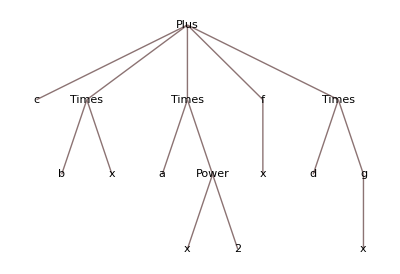

```mathematica
expr//TreeForm
```

```mathematica
expr[[1]]
```

c

```mathematica
expr[[5]]
```

d g[x]

```mathematica
expr[[5,2]]
```

g[x]

```mathematica
expr[[5,2,1]]=y
```

y

```mathematica
expr
```

c+b x+a x^2+f[x]+d g[y]

```mathematica
expr//Length
```

5

### Asociaciones

```mathematica
asoc=<|"nombre"->"Mariana","apellido"->"Pérez","edad"->24,color->RGBColor["Teal"],1->7,π->6|>
```

<|nombre→Mariana,apellido→Pérez,edad→24,color→RGBColor[0., 0.5019607843137255, 0.5019607843137255],1→7,π→6|>

Las asociaciones son el equivalente a un diccionario en otros lenguajes y nos permiten acceder a valores por medio de llaves.

```mathematica
asoc["nombre"]
```

Mariana

```mathematica
asoc[["nombre"]]
```

Mariana

```mathematica
asoc[color]
```

RGBColor[0., 0.5019607843137255, 0.5019607843137255]

```mathematica
asoc[[color]]
```

Part::pkspec1: The expression color cannot be used as a part specification.

<|nombre→Mariana,apellido→Pérez,edad→24,color→RGBColor[0., 0.5019607843137255, 0.5019607843137255],1→7,π→6|>⟦color⟧

```mathematica
asoc[1]
```

7

```mathematica
asoc[[1]]
```

Mariana

```mathematica
asoc[π]
```

6

```mathematica
asoc[[π]]
```

Part::pkspec1: The expression π cannot be used as a part specification.

<|nombre→Mariana,apellido→Pérez,edad→24,color→RGBColor[0., 0.5019607843137255, 0.5019607843137255],1→7,π→6|>⟦π⟧

Además podemos utilizar otras funciones especializadas para las asociaciones

```mathematica
Keys[asoc]
```

```mathematica
Values[asoc]
```

```mathematica
KeySort[asoc]
```

### Datasets

```mathematica
data=Dataset[{
<|"class"->"3rd","age"->19,"sex"->"male","survived"->False|>,<|"class"->"1st","age"->Missing[],"sex"->"female","survived"->True|>,<|"class"->"3rd","age"->39,"sex"->"male","survived"->False|>,<|"class"->"1st","age"->18,"sex"->"male","survived"->False|>,<|"class"->"1st","age"->48,"sex"->"male","survived"->False|>,<|"class"->"1st","age"->30,"sex"->"female","survived"->True|>,<|"class"->"2nd","age"->20,"sex"->"male","survived"->True|>,<|"class"->"3rd","age"->32,"sex"->"male","survived"->False|>,<|"class"->"3rd","age"->39,"sex"->"male","survived"->False|>,<|"class"->"1st","age"->23,"sex"->"female","survived"->True|>
}]
```

Los Datasets son conjuntos de datos organizados especializados para el análisis de datos.

```mathematica
Query[All,"class"]@data
```

```mathematica
Query[Select[#sex=="male"&],"age"]@data
```

```mathematica
Query[All,{"class","survived"}]@data
```

Estos pueden ser más complicados que simplemente datos tabulares al costo de una menor eficiencia computacional.

```mathematica
ExampleData[{"Dataset","StatePopulations"}]
```

Dataset[<>]

### Más estructuras de datos

Además de eso tenemos estructuras de datos más variadas que solo se comentarán y se mostrará un ejemplo, pero no se detallarán

Para arreglos de datos con pocos elementos relativos al tamaño del mismo

```mathematica
SparseArray[{{i_,i_}->-2,{i_,j_}/;Abs[i-j]==1->1},{5,5}]
```

Para operaciones más eficientes con tipos de datos «estándar»

```mathematica
NumericArray[Table[2^i-1,{i,0,8}],"UnsignedInteger8"]
```

```mathematica
Graph[Table[i->Mod[i^2,74],{i,100}]]
```

Para representar datos jerarquizados

```mathematica
Tree[a,{Tree[b,{c,d}],e,f}]
```

Y de manera más general una gran variedad de estructuras nativas que podemos usar en Mathematica

```mathematica
CreateDataStructure["Stack"]
```

Esta es la alternativa a Dataset que solo representa datos tabulares, pero con operaciones más eficientes. Al haber salido en la ultima versión de Mathematica solo la mencionaremos por completitud con los ejemplos anteriores

```mathematica
Tabular[]
```

## Bucles

### Do

```mathematica
?Do
```

Similar a un Table, con la diferencia de que no devuelve nada por sí mismo.

```mathematica
Do[i^2,{i,1,10}]
```

En el caso en el que se desea generar una lista como resultado, Table lo hace directamente, mientras que Do solo puede modificar listas previamente existentes.

```mathematica
cuadrados={};
Do[
AppendTo[cuadrados,i^2],
{i,1,10}
];
cuadrados
```

Útil cuando se quiere obtener el resultado final después de repetir una acción, sin recolectar resultados intermedios.

```mathematica
{a,b}={0,1};
Do[
{a,b}={b,a+b},
10-1
];
b
```

### While

```mathematica
?While
```

Repite una acción mientras se cumpla una condición. Tampoco devuelve nada por sí mismo.

```mathematica
cuadrados={};
i=1;
While[
i<=10,
AppendTo[cuadrados,i^2];
i++
];
cuadrados
```

```mathematica
{a,b}={0,1};
i=1;
While[
i<10,
{a,b}={b,a+b};
i++
];
b
```

### For

```mathematica
?For
```

Combina inicialización, condición y actualización en una sola línea. Tampoco devuelve nada por sí mismo.

```mathematica
cuadrados={};
For[
i=1,i<=10,i++,
AppendTo[cuadrados,i^2]
];
cuadrados
```

```mathematica
{a,b}={0,1};
For[
i=1,i<10,i++,
{a,b}={b,a+b}
];
b
```

## Resumen de la clase

### Estructuras de datos

Las estructuras de datos son formas de organizar y almacenar datos para que puedan utilizarse de manera eficiente.

Existen diversas estructuras de datos como las listas, expresiones, asociaciones, datasets, etc.

#### Listas

Las listas son la estructura fundamental de Wolfram Language y representan colecciones de elementos. Se definen usando llaves {} y separando los elementos con comas. Pueden contener cualquier tipo de datos.

El acceso a los elementos se realiza con doble corchete ⟦⟧ , empezando desde el índice 1.

Saber cómo crear y manipular listas de manera adecuada permite escribir buen código en Wolfram Language y  aprovechar su potencial al máximo.

#### Expresiones

Toda entrada en Mathematica es internamente una expresión.

#### Asociaciones

Equivalentes a diccionarios: permiten acceso a datos mediante llaves.

#### Datasets

Permiten trabajar con datos tabulares y estructuras jerárquicas.

Poseen una sintaxis rica para hacer consultas, transformaciones y visualizaciones.

Más complejos que las listas, pero pueden ser menos eficientes en cómputo .

### Table

Genera listas mediante una expresión repetida un número determinado de veces.

Es declarativo, más eficiente y más fácil de combinar con programación funcional.

### Bucles

No devuelven nada por sí mismos.

#### Do

Se usa para modificar estructuras existentes o generar efectos secundarios (por ejemplo, imprimir, acumular en variables).

Ideal cuando se necesita ejecutar una acción repetidamente sin necesidad de recolectar resultados.

#### While

Ejecuta un bloque de código mientras se cumpla una condición lógica.

Es útil cuando no se conoce de antemano cuántas iteraciones se necesitan.

#### For

Permite combinar inicialización, condición de parada y actualización en una sola instrucción.

Menos recomendable que Table o Do en estilo idiomático de Mathematica.

## Ejemplos

#### Comparación Do vs. Table

Cuál es mejor depende de la tarea que se quiere realizar. En el caso de crear listas, Table es por lo general la mejor opción pues crea una lista como resultado directamente y se usa naturalmente con otras funciones funcionales (que se verán en la próxima clase). Además, el código con Table suele ser más corto y claro.

```mathematica
RepeatedTiming[Table[i^2,{i,1,10}];]
```

```mathematica
RepeatedTiming[
Module[{cuadrados},
cuadrados={};
Do[
AppendTo[cuadrados,i^2],
{i,1,10}
];
cuadrados
];
]
```

A pesar de lo anterior, Do puede ser más rápido en situaciones donde solo se requiera el resultado final luego de repetir una acción.

```mathematica
RepeatedTiming[
Last@Module[{a,b},
{a,b}={0,1};
Table[
{a,b}={b,a+b};
a,
{10-1}
]
];
]
```

```mathematica
RepeatedTiming[
Module[{a,b},
{a,b}={0,1};
Do[
{a,b}={b,a+b},
10-1
];
b;
]
]
```